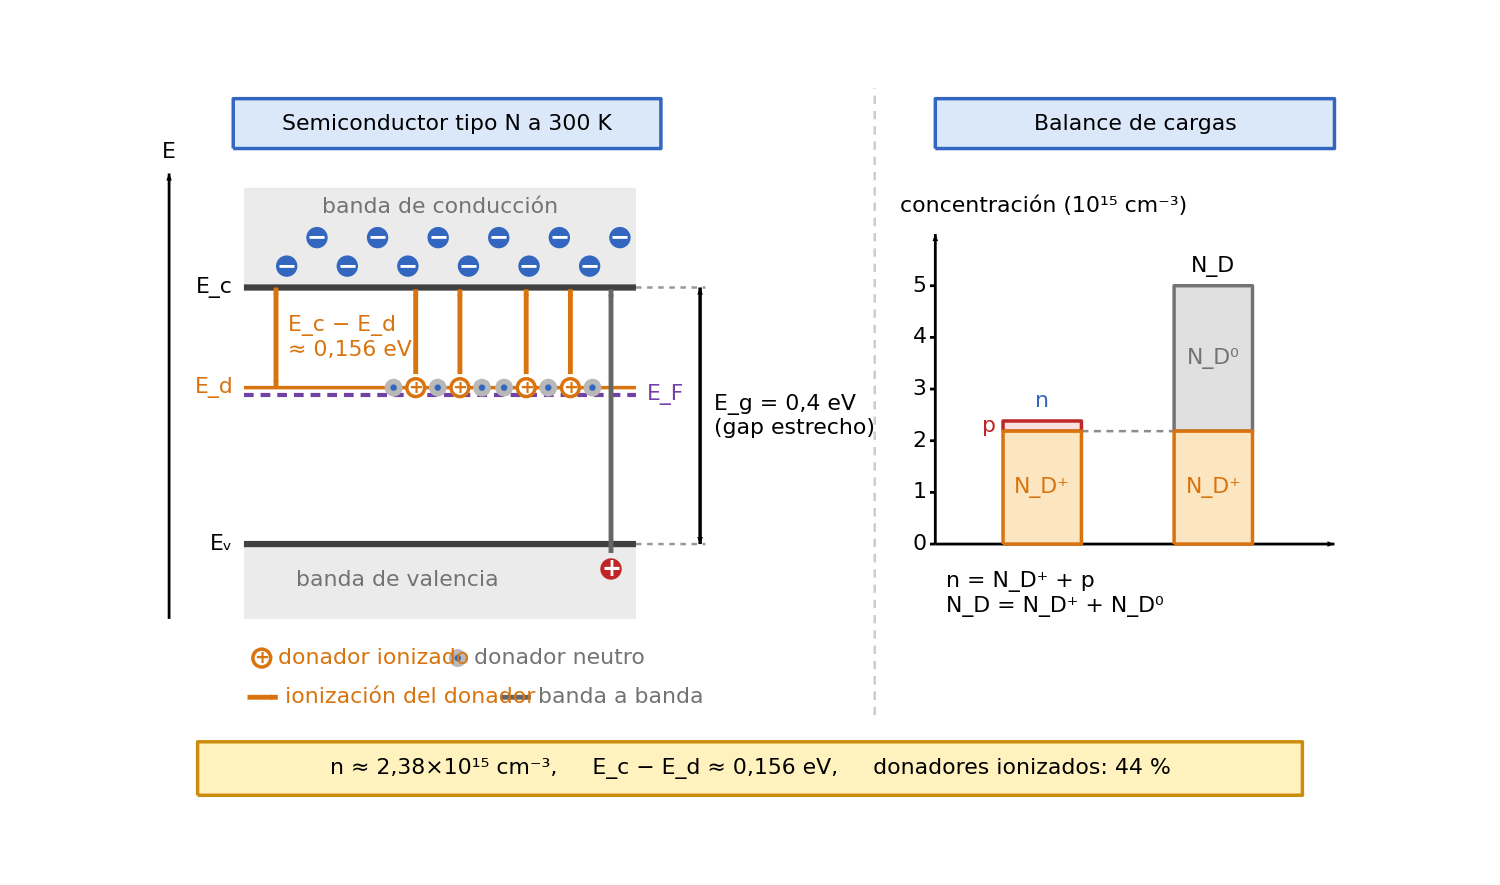

```mathematica
diagramaDonadores = Module[
  {fs, mostrarValores, cAzul, cAzulB, cRojo, cRojoF, cNar, cNarF, cVio, cGris, cOro, cOroB,
   kT, Eg, Nc, Ndon, e, sig, mun, mup, gd, ni2, bq, cq, pp, nn, Ndp, Nd0, dE, EcEF, Ed, EF,
   nIon, idxIon, pct, se, yv, yy, px, Lw, xD, xH, oxB, hu, xA, xB, hw, yb,
   ins, insI, insD, caja, flecha, carga, donIon, donNeu, dec, cient, lblEd, concl},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta los valores calculados (n, Ec-Ed, % ionizado) *)
  cAzul  = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo  = RGBColor[0.75, 0.15, 0.15];  cRojoF = RGBColor[0.98, 0.88, 0.88];
  cNar   = RGBColor[0.85, 0.45, 0.05];  cNarF  = RGBColor[0.99, 0.90, 0.76];
  cVio   = RGBColor[0.45, 0.25, 0.65];  cGris  = GrayLevel[0.45];
  cOro   = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del problema y resolución (eV, cm^-3) ---------- *)
  kT = 0.026;  Eg = 0.4;  Nc = 1.5*10^18;  Ndon = 5.*10^15;
  e = 1.6*10^-19;  sig = 1.;  mun = 2500.;  mup = 1500.;  gd = 2;
  ni2 = Nc^2 Exp[-Eg/kT];                    (* Nc = Nv *)
  bq = sig/(e mup);  cq = (mun/mup) ni2;
  pp = (bq - Sqrt[bq^2 - 4 cq])/2;           (* raíz con n > p (tipo N) *)
  nn = ni2/pp;
  Ndp = nn - pp;  Nd0 = Ndon - Ndp;          (* donadores ionizados y neutros *)
  dE = kT Log[Nd0 Nc/(gd nn Ndp)];           (* Ec - Ed *)
  EcEF = kT Log[Nc/nn];                      (* Ec - EF *)
  Ed = Eg - dE;  EF = Eg - EcEF;             (* energías medidas desde Ev *)
  nIon = Round[10 Ndp/Ndon];                 (* de 10 donadores dibujados, cuántos ionizados *)
  idxIon = Table[Round[(j - 0.5) 10/nIon - 0.5], {j, 1, nIon}];
  pct = Round[100 Ndp/Ndon];

  (* ---------- Geometría ---------- *)
  se = 18;  yv = 1.2;  yy[en_] := yv + se en;   (* escala vertical: energía en eV *)
  px = 3.0;  Lw = 11.0;                          (* bandas *)
  xD[k_] := 7.2 + 0.62 k;                        (* posición de los donadores *)
  xH = 13.3;                                     (* hueco y excitación banda a banda *)
  {oxB, hu} = {22.4, 1.45};                      (* panel derecho: origen y escala *)
  {xA, xB, hw} = {25.4, 30.2, 1.1};              (* centros y semianchura de las barras *)
  yb[c_] := yv + hu c/10.^15;

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  flecha[p1_, p2_, col_, s_: 0.012] :=
    {col, AbsoluteThickness[3.5], Arrowheads[s], Arrow[{p1, p2}]};
  carga[pos_, signo_, col_] :=
    {col, Disk[pos, 0.3], Text[Style[signo, Round[1.1 fs], Bold, White], pos]};
  donIon[pos_] :=
    {White, Disk[pos, 0.25], cNar, AbsoluteThickness[2.5], Circle[pos, 0.25],
     Text[Style["+", Round[0.8 fs], Bold, cNar], pos]};
  donNeu[pos_] := {GrayLevel[0.72], Disk[pos, 0.25], cAzulB, Disk[pos, 0.09]};
  dec[x_, k_] := NumberForm[x, {5, k}, NumberPoint -> ","];
  cient[x_] := Module[{ex = Floor[Log10[x]]},
    Row[{NumberForm[x/10.^ex, {3, 2}, NumberPoint -> ","], "×",
      Superscript["10", ex]}]];

  (* ---------- Textos que dependen de los valores calculados ---------- *)
  lblEd = If[mostrarValores,
    Column[{Row[{Subscript["E", "c"], " − ", Subscript["E", "d"]}],
      Row[{"≈ ", dec[dE, 3], " eV"}]}, Center],
    Row[{Subscript["E", "c"], " − ", Subscript["E", "d"]}]];
  concl = If[mostrarValores,
    Row[{Style["n", Italic], " ≈ ", cient[nn], " ",
      Superscript["cm", "−3"], ",     ",
      Subscript["E", "c"], " − ", Subscript["E", "d"], " ≈ ",
      dec[dE, 3], " eV,     donadores ionizados: ", pct, " %"}],
    "donadores parcialmente ionizados a 300 K"];

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* cabeceras y separador *)
    caja[{8.7, 13.0}, {12.0, 1.4}, cAzul, cAzulB],
    ins["Semiconductor tipo N a 300 K", {8.7, 13.0}],
    caja[{28.0, 13.0}, {11.2, 1.4}, cAzul, cAzulB],
    ins["Balance de cargas", {28.0, 13.0}],
    {GrayLevel[0.8], AbsoluteThickness[1.8], AbsoluteDashing[{6, 5}],
     Line[{{20.7, -3.6}, {20.7, 14.0}}]},

    (* ===== Panel izquierdo: bandas de energía ===== *)
    {Black, AbsoluteThickness[2], Arrowheads[0.014], Arrow[{{0.9, -0.9}, {0.9, 11.6}}]},
    ins[Style["E", Italic], {0.9, 12.2}],
    {GrayLevel[0.92], EdgeForm[None],
     Rectangle[{px, yy[Eg]}, {px + Lw, yy[Eg] + 2.8}],
     Rectangle[{px, yv - 2.1}, {px + Lw, yv}]},
    {GrayLevel[0.25], AbsoluteThickness[4.5],
     Line[{{px, yy[Eg]}, {px + Lw, yy[Eg]}}], Line[{{px, yv}, {px + Lw, yv}}]},
    ins["banda de conducción", {px + Lw/2, yy[Eg] + 2.25}, cGris],
    ins["banda de valencia", {px + Lw/2 - 1.2, yv - 1.0}, cGris],
    insD[Row[{Subscript["E", "c"]}], {px - 0.3, yy[Eg]}],
    insD[Row[{Subscript["E", "d"]}], {px - 0.3, yy[Ed]}, cNar],
    insD[Row[{Subscript["E", "v"]}], {px - 0.3, yv}],

    (* nivel de Fermi y nivel donador *)
    {cVio, AbsoluteThickness[3], AbsoluteDashing[{7, 5}],
     Line[{{px, yy[EF]}, {px + Lw, yy[EF]}}]},
    {cNar, AbsoluteThickness[2.5], Line[{{px, yy[Ed]}, {px + Lw, yy[Ed]}}]},
    insI[Row[{Subscript["E", "F"]}], {px + Lw + 0.3, yy[EF]}, cVio],

    (* energía de activación Ec - Ed *)
    {cNar, AbsoluteThickness[3.5], Arrowheads[{-0.012, 0.012}],
     Arrow[{{3.9, yy[Ed]}, {3.9, yy[Eg]}}]},
    insI[lblEd, {4.25, (yy[Ed] + yy[Eg])/2}, cNar],

    (* banda prohibida *)
    {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
     Line[{{px + Lw, yv}, {15.95, yv}}], Line[{{px + Lw, yy[Eg]}, {15.95, yy[Eg]}}]},
    {Black, AbsoluteThickness[2.5], Arrowheads[{-0.012, 0.012}],
     Arrow[{{15.8, yv}, {15.8, yy[Eg]}}]},
    insI[Column[{Row[{Subscript["E", "g"], " = ", dec[Eg, 1], " eV"}],
       "(gap estrecho)"}, Center], {16.2, (yv + yy[Eg])/2}],

    (* donadores: ionizados (aro naranja) y neutros (electrón ligado) *)
    Table[If[MemberQ[idxIon, k], donIon[{xD[k], yy[Ed]}], donNeu[{xD[k], yy[Ed]}]],
     {k, 0, 9}],
    Table[flecha[{xD[k], yy[Ed] + 0.38}, {xD[k], yy[Eg] - 0.05}, cNar, 0.011],
     {k, idxIon}],

    (* electrones libres (muchos) y hueco (uno): proporción n : p ~ 12 : 1 *)
    Table[carga[{4.2 + 1.7 k, yy[Eg] + 0.6}, "−", cAzulB], {k, 0, 5}],
    Table[carga[{5.05 + 1.7 k, yy[Eg] + 1.4}, "−", cAzulB], {k, 0, 5}],
    carga[{xH, yv - 0.7}, "+", cRojo],
    flecha[{xH, yv - 0.25}, {xH, yy[Eg] - 0.05}, GrayLevel[0.4], 0.011],

    (* leyenda *)
    donIon[{3.5, -2.0}], insI["donador ionizado", {3.95, -2.0}, cNar],
    donNeu[{9.0, -2.0}], insI["donador neutro", {9.45, -2.0}, cGris],
    flecha[{3.1, -3.1}, {3.95, -3.1}, cNar, 0.011],
    insI["ionización del donador", {4.15, -3.1}, cNar],
    flecha[{10.2, -3.1}, {11.05, -3.1}, GrayLevel[0.4], 0.011],
    insI["banda a banda", {11.25, -3.1}, cGris],

    (* ===== Panel derecho: balance de cargas (escala lineal) ===== *)
    {Black, AbsoluteThickness[2], Arrowheads[0.014],
     Arrow[{{oxB, yv}, {oxB + 11.2, yv}}], Arrow[{{oxB, yv}, {oxB, 9.9}}]},
    Table[{Black, AbsoluteThickness[2],
      Line[{{oxB - 0.15, yb[k 10.^15]}, {oxB, yb[k 10.^15]}}],
      insD[ToString[k], {oxB - 0.25, yb[k 10.^15]}]}, {k, 0, 5}],
    insI[Row[{"concentración (", Superscript["10", 15], " ",
       Superscript["cm", "−3"], ")"}], {oxB - 1.0, 10.7}],

    (* barra n = N_D^+ + p *)
    {EdgeForm[{AbsoluteThickness[2.5], cNar}], cNarF,
     Rectangle[{xA - hw, yv}, {xA + hw, yb[Ndp]}]},
    {EdgeForm[{AbsoluteThickness[2.5], cRojo}], cRojoF,
     Rectangle[{xA - hw, yb[Ndp]}, {xA + hw, yb[nn]}]},
    ins[Row[{Subsuperscript["N", "D", "+"]}], {xA, (yv + yb[Ndp])/2}, cNar],
    insD[Style["p", Italic], {xA - hw - 0.2, (yb[Ndp] + yb[nn])/2}, cRojo],
    ins[Style["n", Italic], {xA, yb[nn] + 0.55}, cAzulB],

    (* barra N_D = N_D^+ + N_D^0 *)
    {EdgeForm[{AbsoluteThickness[2.5], cNar}], cNarF,
     Rectangle[{xB - hw, yv}, {xB + hw, yb[Ndp]}]},
    {EdgeForm[{AbsoluteThickness[2.5], cGris}], GrayLevel[0.88],
     Rectangle[{xB - hw, yb[Ndp]}, {xB + hw, yb[Ndon]}]},
    ins[Row[{Subsuperscript["N", "D", "+"]}], {xB, (yv + yb[Ndp])/2}, cNar],
    ins[Row[{Subsuperscript["N", "D", "0"]}], {xB, (yb[Ndp] + yb[Ndon])/2}, cGris],
    ins[Row[{Subscript["N", "D"]}], {xB, yb[Ndon] + 0.55}],
    {GrayLevel[0.55], AbsoluteThickness[1.8], AbsoluteDashing[{5, 4}],
     Line[{{xA + hw, yb[Ndp]}, {xB - hw, yb[Ndp]}}]},

    (* relaciones de balance *)
    insI[Column[{
       Row[{Style["n", Italic], " = ", Subsuperscript["N", "D", "+"], " + ",
         Style["p", Italic]}],
       Row[{Subscript["N", "D"], " = ", Subsuperscript["N", "D", "+"], " + ",
         Subsuperscript["N", "D", "0"]}]}, Left], {oxB + 0.3, -0.2}],

    (* conclusión *)
    caja[{17.2, -5.1}, {31.0, 1.5}, cOro, cOroB],
    ins[concl, {17.2, -5.1}]
   },
   ImageSize -> 1500,
   PlotRange -> {{0, 34.4}, {-6.1, 14.2}},
   PlotRangePadding -> None,
   AspectRatio -> 20.3/34.4,
   Background -> White]
];
diagramaDonadores
```